```mathematica
init = CenterArray[1, {200, 200}] ;
s = ReplacePart[init, {99, 100}->1];
ArrayPlot@s
```

-Graphics-

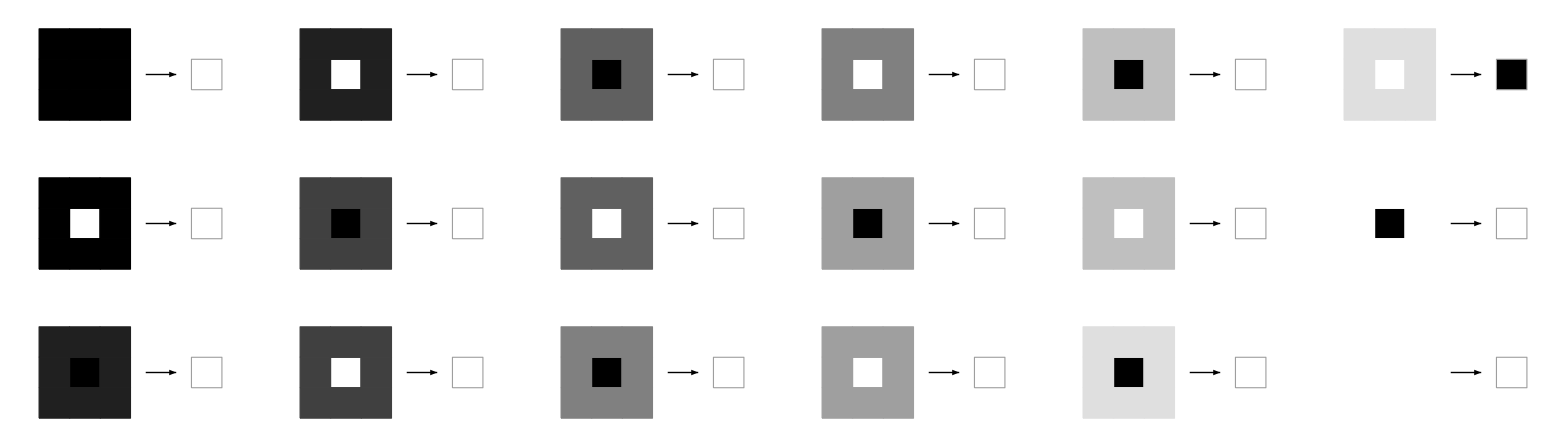

```mathematica
RulePlot[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->4|>]]
```

```mathematica
ArrayPlot@CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->4|>,s, {{{1}}}]
```

-Graphics-

```mathematica
Position[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->4|>,s, {{{1}}}], 1]
```

{{23,24},{23,25},{23,26},{26,24},{26,25},{26,26}}

```mathematica
RandomChoice@Position[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->4|>,s, {{{1}}}], 1]
```

{26,24}

```mathematica
ArrayPlot@Nest[ReplacePart[#,RandomChoice@Position[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->76|>,#, {{{1}}}], 1]-> 1]&,s, 10000]
```

-Graphics-